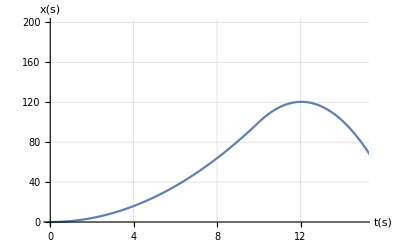

```mathematica
f1 = t^2;
f2 = 100-4.9(t-10)^2+20(t-10);



p1=Plot[f1,{t,0,10}];
p2=Plot[f2,{t,10,17}];


Show[{p1,p2}, PlotRange ->{{0,15},{0,200}}, AxesOrigin->{0,0}, AxesLabel->{t[s],x[s]},LabelStyle->{FontSize 12},GridLines-> Automatic,GridLinesStyle ->Directive[Dashed]]
```